# Plot functions

```mathematica
cef={ChartElementData["BoxWhisker"][##],EdgeForm[],FaceForm[],ChartElementData["PointDensity","PointStyle"->Directive[EdgeForm[Black],Opacity[.05],PointSize[.1],Charting`ChartStyleInformation["Color"]]][##]}&;
```

```mathematica
Bij = "β_0";
Sx = "ω_x";
gij = "γ_0";
purp=RGBColor[0.42, 0.21, 0.73];
gree=RGBColor[0.41000000000000003, 0.71, 0.];
rec =RGBColor[0.76, 0, 0];
blu=RGBColor[0.29, 0.47000000000000003, 1.];
```

```mathematica
BoxPlotDev[dm_,dn_,dM_,labs_]:=Module[{},
ps = 0.05;
fm=(1.8-.2)/Length@dm;
fn = (1.8-.2)/Length@dn;
fM = (1.8-.2)/Length@dM;
rm=Range[.2,1.8-fm,fm];
rn=Range[2.2,3.8-fn,fn];
rM=Range[4.2,5.8-fM,fM];
Show[ListLogPlot[Transpose@{rm,dm} ,PlotStyle->Directive[purp, PointSize[ps],Opacity[.30]],
Frame->True,
FrameStyle->Black,
PlotRange->{{0,6},{Min[Flatten@{dm, dn, dM}]-1,Max[Flatten@{dm, dn, dM}]+1}},
FrameLabel->{"","deviations from equilibrium ρ","",""},
FrameTicks->{{(*Range[0,0.8,0.2]*)Automatic,None},{{{1,labs⟦1⟧},{3,labs⟦2⟧},{5,labs⟦3⟧}},None}},
FrameTicksStyle->10,
AspectRatio->GoldenRatio,
ImageSize->{Automatic,200}],
ListLogPlot[Transpose@{rn,dn} ,PlotStyle->Directive[gree, PointSize[ps],Opacity[.3]]],
ListLogPlot[Transpose@{rM,dM} ,PlotStyle->Directive[rec, PointSize[ps],Opacity[.3]]],
ListLogPlot[{{1,Median@dm},{3,Median@dn},{5, Median@dM}}, PlotStyle->Directive[Black, PointSize[0.05]]],
ListLogPlot[{
{1.001,Quantile[dm,1/4]},
{1.001,Quantile[dm,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListLogPlot[{
{3.001,Quantile[dn,1/4]},
{3.001,Quantile[dn,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListLogPlot[{
{5.001,Quantile[dM,1/4]},
{5.001,Quantile[dM,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
]
]
BoxPlotDevd[dm_,dn_,dM_,labs_]:=Module[{},
ps = 0.05;
fm=(1.8-.2)/Length@dm;
fn = (1.8-.2)/Length@dn;
fM = (1.8-.2)/Length@dM;
rm=Range[.2,1.8-fm,fm];
rn=Range[4.2,5.8-fn,fn];
rM=Range[2.2,3.8-fM,fM];
Show[ListLogPlot[Transpose@{rm,dm} ,PlotStyle->Directive[purp, PointSize[ps],Opacity[.30]],
Frame->True,
FrameStyle->Black,
PlotRange->{{0,6},{Min[Flatten@{dm, dn, dM}]-1,Max[Flatten@{dm, dn, dM}]+1}},
FrameLabel->{"","deviations from equilibrium ρ","",""},
FrameTicks->{{(*Range[0,0.8,0.2]*)Automatic,None},{{{1,labs⟦1⟧},{3,labs⟦2⟧},{5,labs⟦3⟧}},None}},
FrameTicksStyle->10,
AspectRatio->GoldenRatio,
ImageSize->{Automatic,200}],
ListLogPlot[Transpose@{rn,dn} ,PlotStyle->Directive[gree, PointSize[ps],Opacity[.3]]],
ListLogPlot[Transpose@{rM,dM} ,PlotStyle->Directive[blu, PointSize[ps],Opacity[.3]]],
ListLogPlot[{{1,Median@dm},{3,Median@dn},{5, Median@dM}}, PlotStyle->Directive[Black, PointSize[0.05]]],
ListLogPlot[{
{1.001,Quantile[dm,1/4]},
{1.001,Quantile[dm,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListLogPlot[{
{3.001,Quantile[dn,1/4]},
{3.001,Quantile[dn,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListLogPlot[{
{5.001,Quantile[dM,1/4]},
{5.001,Quantile[dM,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
]
]
```

```mathematica
BoxPlot[dm_,dn_,dM_,labs_]:=Module[{},
ps = 0.035;
fm=(1.8-.2)/Length@dm;
fn = (1.8-.2)/Length@dn;
fM = (1.8-.2)/Length@dM;
rm=Range[.2,1.8-fm,fm];
rn=Range[2.2,3.8-fn,fn];
rM=Range[4.2,5.8-fM,fM];
Show[ListPlot[Transpose@{rm,dm} ,PlotStyle->Directive[purp, PointSize[ps],Opacity[.10]],PlotRange->{{0,6},{0,.7}},
Frame->True,
FrameStyle->Black,
FrameLabel->{"","early warning score","",""},
FrameTicks->{{Range[0,0.8,0.2],None},{{{1,labs⟦1⟧},{3,labs⟦2⟧},{5,labs⟦3⟧}},None}},
FrameTicksStyle->10,
AspectRatio->GoldenRatio,
ImageSize->{Automatic,200}],
ListPlot[Transpose@{rn,dn} ,PlotStyle->Directive[gree, PointSize[ps],Opacity[.15]]],
ListPlot[Transpose@{rM,dM} ,PlotStyle->Directive[rec, PointSize[ps],Opacity[.15]]],
ListPlot[{{1,Median@dm},{3,Median@dn},{5, Median@dM}}, PlotStyle->Directive[Black, PointSize[0.05]]],
ListPlot[{
{1.001,Quantile[dm,1/4]},
{1.001,Quantile[dm,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{
{3.001,Quantile[dn,1/4]},
{3.001,Quantile[dn,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{
{5.001,Quantile[dM,1/4]},
{5.001,Quantile[dM,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
]
]
BoxPlotd[dm_,dn_,dM_,labs_]:=Module[{},
fm=(1.8-.2)/Length@dm;
fn = (1.8-.2)/Length@dn;
fM = (1.8-.2)/Length@dM;
rm=Range[.2,1.8-fm,fm];
rn=Range[4.2,5.8-fn,fn];
rM=Range[2.2,3.8-fM,fM];
Show[ListPlot[Transpose@{rm,dm} ,PlotStyle->Directive[purp, PointSize[ps],Opacity[.15]],PlotRange->{{0,6},{0,.7}},
FrameLabel->{"","early warning score","",""},
Frame->True,
FrameStyle->Black,
PlotRange->{{0.5,Automatic},{0,0.7}},
FrameTicks->{{Range[0,0.8,0.2],None},{{{1,labs⟦1⟧},{3,labs⟦2⟧},{5,labs⟦3⟧}},None}},
FrameTicksStyle->10,
AspectRatio->GoldenRatio,
ImageSize->{Automatic,200}],
ListPlot[Transpose@{rn,dn} ,PlotStyle->Directive[gree, PointSize[ps],Opacity[.15]]],
ListPlot[Transpose@{rM,dM} ,PlotStyle->Directive[blu, PointSize[ps],Opacity[.15]]],
ListPlot[{{1,Median@dm},{5,Median@dn},{3, Median@dM}}, PlotStyle->Directive[Black, PointSize[0.05]]],
ListPlot[{
{1.001,Quantile[dm,1/4]},
{1.001,Quantile[dm,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{
{5.001,Quantile[dn,1/4]},
{5.001,Quantile[dn,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{
{3.001,Quantile[dM,1/4]},
{3.001,Quantile[dM,3/4]}1
},Joined->True,PlotStyle->Directive[Black]]
]
]
```

```mathematica
ScatPlot[dm_,dn_,dM_,ylab_]:=Module[{},
Table[
data=dm⟦ordernetworks⟧⟦i⟧;
datan=dn⟦ordernetworks⟧⟦i⟧;
dataM=dM⟦ordernetworks⟧⟦i⟧;
mind = Min[{data, datan, dataM}];
maxd = Max[{data, datan, dataM}];
Show[
ListPlot[{{i,data}},
 PlotStyle->Directive[purp, PointSize[0.017]],
PlotRange->{{0,52},{-1,1}},
Frame->{True,True,False, False},
FrameStyle->Black,
FrameTicksStyle->10,
FrameLabel->{"network label",ylab,"",""},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,None}},
AspectRatio->0.2,
ImageSize->{Automatic,100}
],
ListPlot[Thread[{i,{mind,maxd}}],
PlotStyle->Directive[RGBColor[0.59, 0.59, 0.59]],
 Joined->True],
ListPlot[{{i,dataM}},
PlotStyle->Directive[rec, PointSize[0.015]]
],
ListPlot[{{i,datan}},
PlotStyle->Directive[gree, PointSize[0.012]]
(*PlotRange->{{0,1},{0,Length@dataR+1}},*)
]
]
,{i,1,51}]//Show
]
ScatPlotd[dm_,dn_,dM_,ylab_]:=Module[{},
Table[
data=dm⟦ordernetworks⟧⟦i⟧;
datan=dn⟦ordernetworks⟧⟦i⟧;
dataM=dM⟦ordernetworks⟧⟦i⟧;
mind = Min[{data, datan, dataM}];
maxd = Max[{data, datan, dataM}];
Show[
ListPlot[{{i,data}},
 PlotStyle->Directive[purp, PointSize[0.017]],
PlotRange->{{0,52},{-1,1}},
Frame->{True,True,False, False},
FrameStyle->Black,
FrameTicksStyle->10,
FrameLabel->{"network label",ylab,"",""},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,None}},
AspectRatio->0.2,
ImageSize->{Automatic,100}
],
ListPlot[Thread[{i,{mind,maxd}}],
PlotStyle->Directive[RGBColor[0.59, 0.59, 0.59]],
 Joined->True],
ListPlot[{{i,dataM}},
PlotStyle->Directive[blu, PointSize[0.015]]
],
ListPlot[{{i,datan}},
PlotStyle->Directive[gree, PointSize[0.012]]
(*PlotRange->{{0,1},{0,Length@dataR+1}},*)
]
]
,{i,1,51}]//Show
]
```

```mathematica
DistPlot[dm_,dn_,dM_]:=Module[{},
Show[
DistributionChart[{dm,dn,dM},
ChartElementFunction->"HistogramDensity",
ImageSize->{180,Automatic},
FrameStyle->Black,
GridLines->{{},{0}},
Frame->{False, True, False, False},
FrameTicks->{{Range[-1,1,0.2],None},{Automatic,None}},
FrameTicksStyle->12,
ChartStyle->{{EdgeForm[None],EdgeForm[None]},{purp,gree,rec}},
AspectRatio->GoldenRatio
],
ListPlot[{Median@dm,Median@dn, Median@dM}, PlotStyle->Directive[Black, PointSize[0.06]]]
,
ListPlot[{
{1.001,Quantile[dm,1/4]},
{1.001,Quantile[dm,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
,
ListPlot[{
{2.001,Quantile[dn,1/4]},
{2.001,Quantile[dn,3/4]}
},Joined->True,PlotStyle->Directive[Black]],
ListPlot[{
{3.001,Quantile[dM,1/4]},
{3.001,Quantile[dM,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
]
]
```

# Import data

```mathematica
filenames = {"M_SD_001","M_SD_002","M_SD_003","M_SD_008","M_SD_009","M_SD_011","M_SD_014","M_SD_015","M_SD_017","M_SD_021","M_SD_023","M_SD_031","M_SD_032","M_SD_033","M_SD_010","M_SD_012","M_SD_013","M_SD_020","M_SD_024","M_SD_025","M_SD_026","M_SD_027","M_SD_028","M_SD_029","M_SD_030","M_PL_069_03","M_PL_036","M_PL_069_01","M_PL_067","M_PL_032","M_PL_050","M_PL_071","M_PL_025","M_PL_003","M_PL_039","M_PL_006","M_PL_008","M_PL_011","M_PL_013","M_PL_033","M_PL_037","M_PL_038","M_PL_046","M_PL_059","M_PL_063","M_PL_064","M_PL_065","M_PL_066","M_PL_068","M_PL_069_02","M_PL_070"};
NetsN = Length@filenames;
ordernetworks = {43,35,49,36,37,10,48,47,18,2,38,41,14,33,1,46,44,29,17,15,28,19,45,3,12,31,30,27,20,5,16,42,13,26,11,23,22,24,25,8,39,9,4,32,50,34,40,51,7,6,21};
```

```mathematica
SetDirectory[NotebookDirectory[]];
SS = Import["data_FigS8/NetStructure/SSall.mx"];
Deg = Import["data_FigS8/NetStructure/Degree.mx"];
MSSsize =  Import["data_FigS8/NetStructure/MSSsize.mx"];
MaxSS = Import["data_FigS8/NetStructure/MaxSS.csv"]//Flatten;
SkewnessSS = Table[
Skewness[SS⟦network⟧]
,{network, 1, Length@SS}];
```

```mathematica
dirnom="data_GeneralFigs/";
EWS = Table[Table[Import[dirnom<>j<>"EWS"<>ToString[i]<>".csv","Table"],{i,0,13}],{j,filenames⟦1;;51⟧}];
```

```mathematica
numsrep={"01","02","03","04","05","06","07","08","09","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40","41","42","43","44","45","46","47","48","49","50"};
SetDirectory["data_FigS8/EWSdata"];
existData=FileNames[];
```

```mathematica
EWSb00 =Table[DeleteCases[Table[thisFile = j<>"_EWS_B00_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
EWSb01 =Table[DeleteCases[Table[thisFile = j<>"_EWS_B01_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
```

```mathematica
EWSg00 =Table[DeleteCases[Table[thisFile = j<>"_EWS_g00_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
EWSg01 =Table[DeleteCases[Table[thisFile = j<>"_EWS_g01_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
```

```mathematica
EWSd0 =Table[DeleteCases[Table[thisFile = j<>"_EWS_d0_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
EWSd1 =Table[DeleteCases[Table[thisFile = j<>"_EWS_d1_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
```

```mathematica
EWSh0 =Table[DeleteCases[Table[thisFile = j<>"_EWS_h0_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
EWSh1 =Table[DeleteCases[Table[thisFile = j<>"_EWS_h1_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
```

```mathematica
EWSs0 =Table[DeleteCases[Table[thisFile = j<>"_EWS_s0_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
EWSs1 =Table[DeleteCases[Table[thisFile = j<>"_EWS_s1_"<>ToString[i]<>".csv";
If[MemberQ[existData, thisFile],Import[thisFile,"Table"]//Flatten],{i,numsrep}],Null],{j,filenames}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
QS = Import["data_FigS8/data_q_r1/Qs.csv","Table"];
QR = Import["data_FigS8/data_q_r1/Qr.csv","Table"];
RS = Import["data_FigS8/data_q_r1/Rs.csv","Table"];
RR = Import["data_FigS8/data_q_r1/Rr.csv","Table"];
QD = QS-QR ;
RD = RS - RR;
```

```mathematica
SetDirectory[NotebookDirectory[]];
DevEb00=Import["data_FigS8/devEqData/DevEb00.mx"];
DevEb01=Import["data_FigS8/devEqData/DevEb01.mx"];
DevEg00=Import["data_FigS8/devEqData/DevEg00.mx"];
DevEg01=Import["data_FigS8/devEqData/DevEg01.mx"];
DevEd0=Import["data_FigS8/devEqData/DevEd0.mx"];
DevEd1=Import["data_FigS8/devEqData/DevEd1.mx"];
DevEh0=Import["data_FigS8/devEqData/DevEh0.mx"];
DevEh1=Import["data_FigS8/devEqData/DevEh1.mx"];
DevEs0=Import["data_FigS8/devEqData/DevEs0.mx"];
DevEs1=Import["data_FigS8/devEqData/DevEs1.mx"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
DevEb00a=Import["data_FigS8/devEqData/DevEb00a.mx"];
DevEb01a=Import["data_FigS8/devEqData/DevEb01a.mx"];
DevEg00a=Import["data_FigS8/devEqData/DevEg00a.mx"];
DevEg01a=Import["data_FigS8/devEqData/DevEg01a.mx"];
DevEd0a=Import["data_FigS8/devEqData/DevEd0a.mx"];
DevEd1a=Import["data_FigS8/devEqData/DevEd1a.mx"];
DevEh0a=Import["data_FigS8/devEqData/DevEh0a.mx"];
DevEh1a=Import["data_FigS8/devEqData/DevEh1a.mx"];
DevEs0a=Import["data_FigS8/devEqData/DevEs0a.mx"];
DevEs1a=Import["data_FigS8/devEqData/DevEs1a.mx"];
```

```mathematica
DevEn = Table[Dev=Import["data_FigS8/devEqData/"<>j<>"DevEqO2_reps.csv","Table"]//Flatten;
Dev⟦1;;14⟧,{j,filenames⟦1;;51⟧}];
```

# Fig S8

## MakePLots

## EWS

```mathematica
dn = Flatten@EWS;
dm = Flatten@EWSb00;
dM = Flatten@EWSb01;
EWB=BoxPlot[dm,dn,dM,{Bij<>"=1",Bij<>"=2",Bij<>"=3"}];
dm = Flatten@EWSd0;
dM = Flatten@EWSd1;
EWd=BoxPlot[dm,dn,dM,{"δ=.25","δ=0.5","δ=1"}];
dm = Flatten@EWSg00;
dM = Flatten@EWSg01;
EWg=BoxPlot[dm,dn,dM,{gij<>"=80",gij<>"=120",gij<>"=160"}];
dm = Flatten@EWSh0;
dM = Flatten@EWSh1;
EWh=BoxPlot[dm,dn,dM,{ "h=0.001","h=0.01","h=0.1"}];
dm = Flatten@EWSs0;
dM = Flatten@EWSs1;
EWs=BoxPlotd[dm,dn,dM,{ Sx<>"=0.1", Sx<>"=1",Sx<>"=10"}];
```

## DevsEq

```mathematica
dn = Flatten@DevEn;
dm = Flatten@DevEb00a;
dM = Flatten@DevEb01a;
DevplotB=BoxPlotDev[dm,dn,dM,{Bij<>"=1",Bij<>"=2",Bij<>"=3"}];
(*Export["fig/DevB.eps",DevplotB];*)
dm = Flatten@DevEd0a;
dM = Flatten@DevEd1a;
Devplotd=BoxPlotDev[dm,dn,dM,{"δ=.25","δ=0.5","δ=1"}];
(*Export["fig/Devd.eps",Devplotd];*)
dm = Flatten@DevEg00a;
dM = Flatten@DevEg01a;
Devplotg=BoxPlotDev[dm,dn,dM,{gij<>"=80",gij<>"=120",gij<>"=160"}];
(*Export["fig/Devg.eps",Devplotg];*)
dm = Flatten@DevEh0a;
dM = Flatten@DevEh1a;
Devploth=BoxPlotDev[dm,dn,dM,{ "h=0.001","h=0.01","h=0.1"}];
(*Export["fig/Devh.eps",Devploth];*)
dm = Flatten@DevEs0a;
dM = Flatten@DevEs1a;
Devplots=BoxPlotDevd[dm,dn,dM,{ Sx<>"=0.1", Sx<>"=1",Sx<>"=10"}];
(*Export["fig/Devs.eps",Devplots];*)
```

## delta

### q

```mathematica
dn=QD⟦All,1⟧;

dm = Flatten@QD⟦All,2⟧;
dM = Flatten@QD⟦All,3⟧;
(*QDB=DistPlot[dm,dn,dM];*)
QDBs=ScatPlot[dm,dn,dM,"q-(q^*)_rand"];

dm = Flatten@QD⟦All,4⟧;
dM = Flatten@QD⟦All,5⟧;
(*QDg=DistPlot[dm,dn,dM];*)
QDgs=ScatPlot[dm,dn,dM,"q-(q^*)_rand"];

dm = Flatten@QD⟦All,6⟧;
dM = Flatten@QD⟦All,7⟧;
(*QDd=DistPlot[dm,dn,dM];*)
QDds=ScatPlot[dm,dn,dM,"q-(q^*)_rand"];

dm = Flatten@QD⟦All,8⟧;
dM = Flatten@QD⟦All,9⟧;
(*QDh=DistPlot[dm,dn,dM];*)
QDhs=ScatPlot[dm,dn,dM,"q-(q^*)_rand"];

dm = Flatten@QD⟦All,10⟧;
dM = Flatten@QD⟦All,11⟧;
(*QDs=DistPlot[dm,dn,dM];*)
QDss=ScatPlotd[dm,dn,dM,"q-(q^*)_rand"];
```

```mathematica
dn=QD⟦All,1⟧;
dm = Flatten@QD⟦All,10⟧;
dM = Flatten@QD⟦All,11⟧;
(*QDs=DistPlot[dm,dn,dM];*)
QDss=ScatPlotd[dm,dn,dM,"q-(q^*)_rand"]
```

### r

```mathematica
dn=RD⟦All,1⟧;

dm = Flatten@RD⟦All,2⟧;
dM = Flatten@RD⟦All,3⟧;
(*RDB=DistPlot[dm,dn,dM];*)
RDBs = ScatPlot[dm,dn,dM,"r_1-r_(1, rand)"];

dm = Flatten@RD⟦All,4⟧;
dM = Flatten@RD⟦All,5⟧;
(*RDg=DistPlot[dm,dn,dM];*)
RDgs = ScatPlot[dm,dn,dM,"r_1-r_(1, rand)"];

dm = Flatten@RD⟦All,6⟧;
dM = Flatten@RD⟦All,7⟧;
(*RDd=DistPlot[dm,dn,dM];*)
RDds = ScatPlot[dm,dn,dM,"r_1-r_(1, rand)"];

dm = Flatten@RD⟦All,8⟧;
dM = Flatten@RD⟦All,9⟧;
(*RDh=DistPlot[dm,dn,dM];*)
RDhs = ScatPlot[dm,dn,dM,"r_1-r_(1, rand)"];

dm = Flatten@RD⟦All,10⟧;
dM = Flatten@RD⟦All,11⟧;
(*RDs=DistPlot[dm,dn,dM];*)
RDss = ScatPlot[dm,dn,dM,"r_1-r_(1, rand)"];
```

```mathematica
dn=RD⟦All,1⟧;
dm = Flatten@RD⟦All,10⟧;
dM = Flatten@RD⟦All,11⟧;
(*RDs=DistPlot[dm,dn,dM];*)
RDss = ScatPlotd[dm,dn,dM,"r_1-r_(1, rand)"];
```

## Show Plots

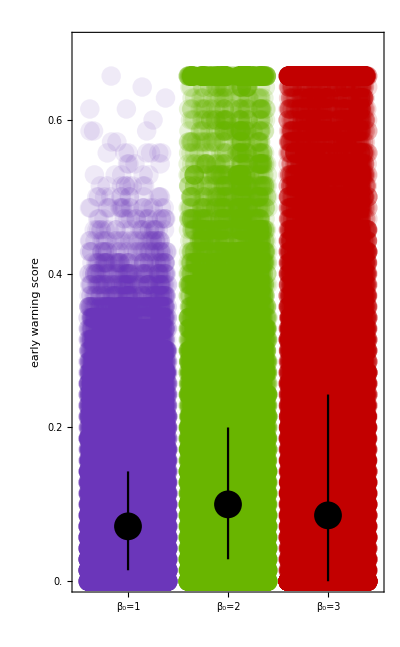
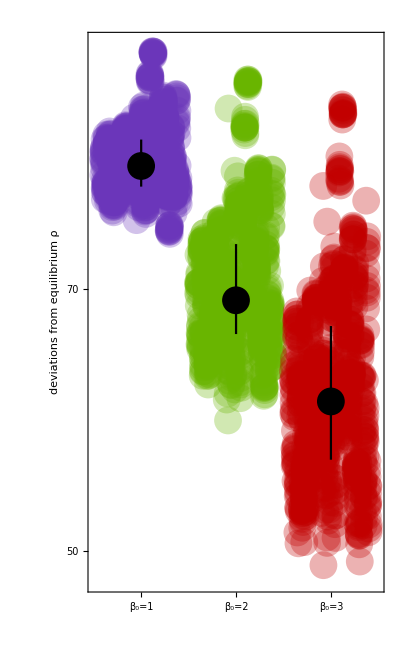

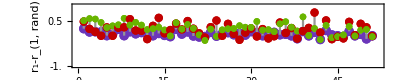

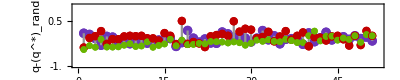

```mathematica
EWB DevplotB 
RDBs 
QDBs
```

```mathematica
(*Export["EWB.eps",EWB];
Export["RDBs.eps",RDBs];
Export["QDBs.eps",QDBs];*)
```

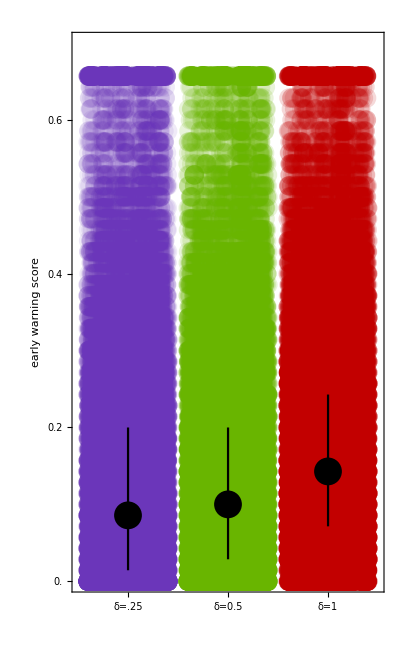
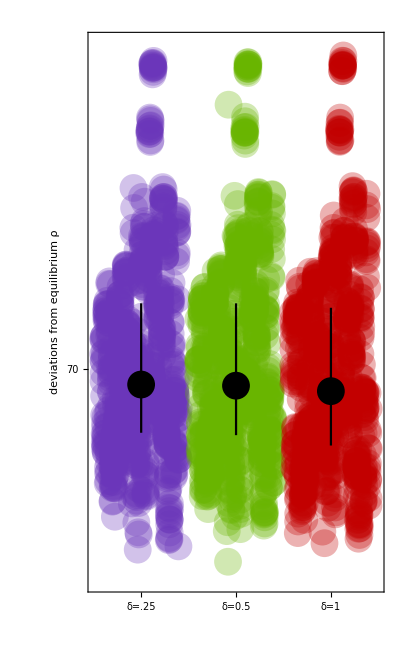

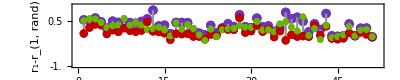

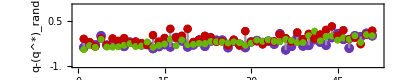

```mathematica
EWd Devplotd
RDds 
QDds
```

```mathematica
(*Export["EWd.eps",EWd];
Export["RDds.eps",RDds];
Export["QDds.eps",QDds];*)
```

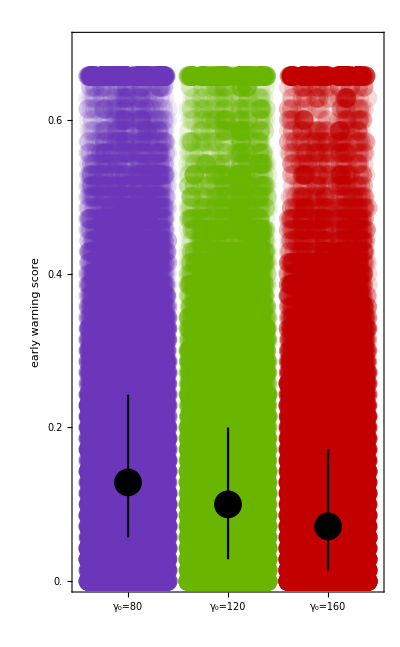
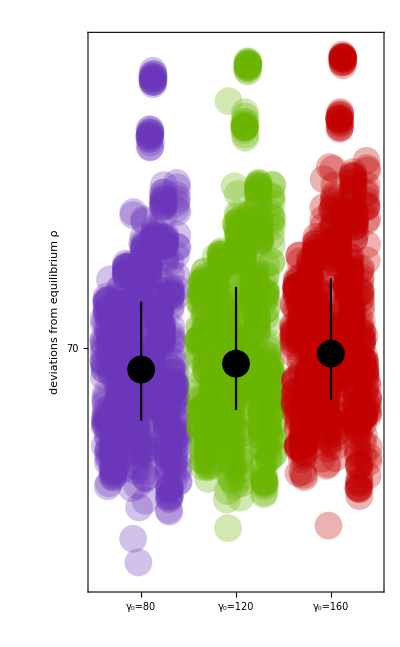

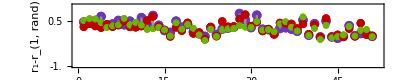

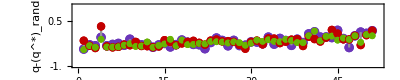

```mathematica
EWg Devplotg 
RDgs 
QDgs
```

```mathematica
(*Export["EWg.eps",EWg];
Export["RDgs.eps",RDgs];
Export["QDgs.eps",QDgs];*)
```

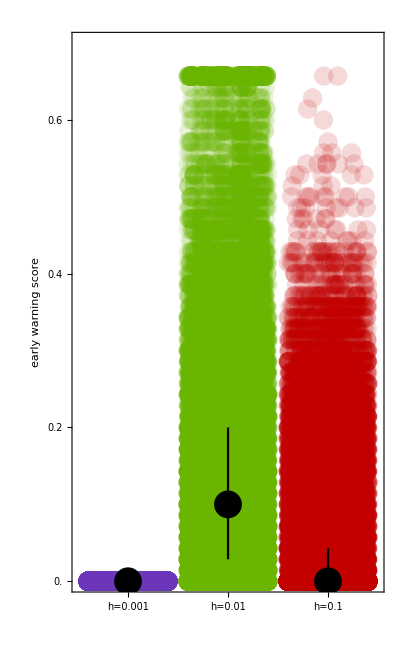
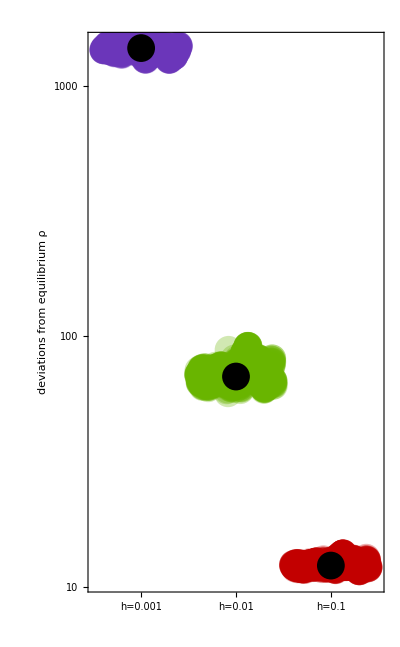

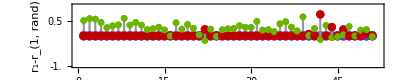

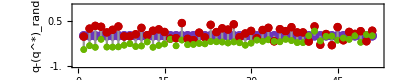

```mathematica
EWh Devploth 
RDhs 
QDhs
```

```mathematica
(*Export["EWh.eps",EWh];
Export["RDhs.eps",RDhs];
Export["QDhs.eps",QDhs];*)
```

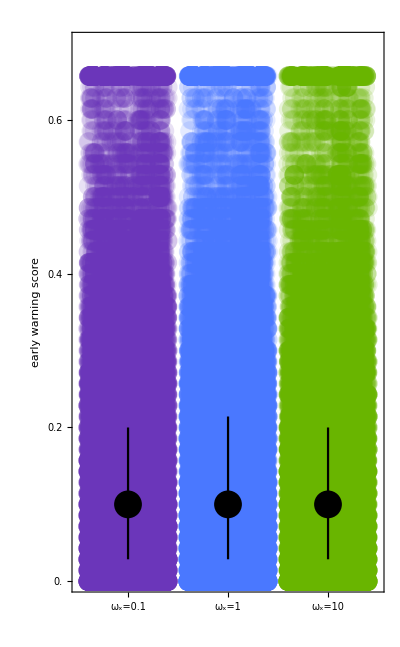
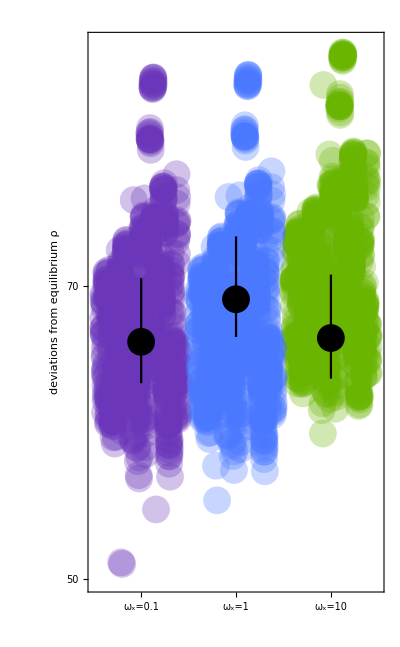

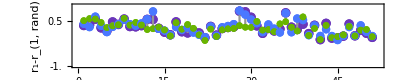

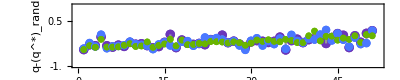

```mathematica
EWs  Devplots
RDss 
QDss
```

```mathematica
(*Export["EWss.eps",EWs];
Export["RDss.eps",RDss];
Export["QDss.eps",QDss];*)
```

# Fig S9

## r_1-r_(1,rand)

### build model

```mathematica
dr=DimensionReduction[Thread[{MaxSS, SkewnessSS}],1,Method->"AutoEncoder"];
```

```mathematica
ρq = Join[DevEb00,DevEb01,DevEg00,DevEg01,DevEd0,DevEd1(*,DevEh0,DevEh1*),DevEs0,DevEs1];
MaxSSe=Table[MaxSS,{8}]//Flatten;
SkewnessSSe=Table[SkewnessSS,{8}]//Flatten;
σq = dr[Thread[{MaxSSe, SkewnessSSe}]]//Flatten;
rData =  Join[RD⟦All,2⟧, RD⟦All,3⟧, RD⟦All,4⟧, RD⟦All,5⟧, RD⟦All,6⟧, RD⟦All,7⟧(*, RD⟦All,8⟧, RD⟦All,9⟧*),  RD⟦All,10⟧, RD⟦All,11⟧];
data = Thread[{σq,ρq, rData}];
(*nlm=NonlinearModelFit[data, a x^2 + b y*x + c y^2+ d,{a,b,c,d},{x,y}];*)
nlm=NonlinearModelFit[data, a x^4 + b y*x + c y^2+ d,{a,b,c,d},{x,y}];
```

### make plot

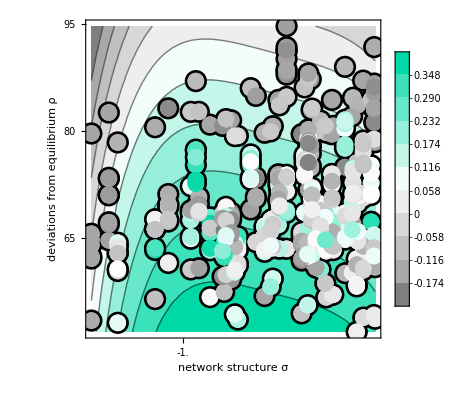

```mathematica
colors=Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},Rescale[#,{Min@rData,Max@rData}]]&/@rData;
Show[
ContourPlot[nlm[x,y],{x, Min@σq, Max@σq},{y,Min@ρq, Max@ρq},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->10,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ","deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,5],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True
(*PlotLegends->Automatic*)
]
,
ListPlot[Thread[{σq,ρq}],
PlotStyle-> Directive[Black, PointSize[0.04],Opacity[1]]
]
,
ListPlot[Partition[Thread[{σq,ρq}],1],
PlotStyle->(Directive[#,PointSize[0.03]]&/@colors)
]
]
```

```mathematica
{"param:",nlm["ParameterPValues"]}
```

{param:,{5.66698×10^-7,0.0739281,3.49826×10^-11,1.20838×10^-29}}

## q*-q*_rand

### build model

```mathematica
qData =  Join[QD⟦All,2⟧, QD⟦All,3⟧, QD⟦All,4⟧, QD⟦All,5⟧, QD⟦All,6⟧, QD⟦All,7⟧,  QD⟦All,10⟧, QD⟦All,11⟧];
data = Thread[{σq,ρq, qData}];
nlm=NonlinearModelFit[data, a x^2 + b y*x + c y^2+ d,{a,b,c,d},{x,y}];
```

### make plot

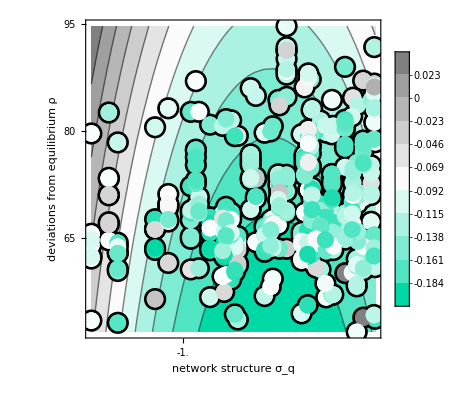

```mathematica
colors=Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{Min@qData,Max@qData}]]&/@qData;
Show[
ContourPlot[nlm[x,y],{x, Min@σq, Max@σq},{y,Min@ρq, Max@ρq},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->10,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ_q","deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,5],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True
(*PlotLegends->Automatic*)
]
,
ListPlot[Thread[{σq,ρq}],
PlotStyle-> Directive[Black, PointSize[0.04],Opacity[1]]
]
,
ListPlot[Partition[Thread[{σq,ρq}],1],
PlotStyle->(Directive[#,PointSize[0.03]]&/@colors)
]
]
```

```mathematica
{"param:",nlm["ParameterPValues"]}
```

{param:,{0.000101962,0.797171,0.0384806,1.89738×10^-11}}